```mathematica
Eqt4 = f^4*xbt + f^3*(1-f)*xi + f^2*(1-f)*xi+f*(1-f)*xi+(1-f)*xi
```

f^4 xbt+(1-f) xi+(1-f) f xi+(1-f) f^2 xi+(1-f) f^3 xi

```mathematica
Eqt5 = f^5*xbt +f^4*(1-f)*xi + f^3*(1-f)*xi + f^2*(1-f)*xi+f*(1-f)*xi+(1-f)*xi
```

f^5 xbt+(1-f) xi+(1-f) f xi+(1-f) f^2 xi+(1-f) f^3 xi+(1-f) f^4 xi

```mathematica
FullSimplify[Eqt4]
```

f^4 (xbt-xi)+xi

```mathematica
FullSimplify[Eqt5]
```

f^5 (xbt-xi)+xi

```mathematica
f^n*f^n
```

f^(2 n)

```mathematica
D[D[(xb-x)^2,x],x]
D[D[x*(xb - x),x],x]
D[D[x^2,x],x]
```

2

-2

2

```mathematica
var = f^(2n)*σ^2-2*f^n*σ^2 + σ^2
```

σ^2-2 f^n σ^2+f^(2 n) σ^2

```mathematica
FullSimplify[var]
```

(-1+f^n)^2 σ^2

```mathematica
(f^n*(xb-x)+x)^2
```

(x+f^n (-x+xb))^2

```mathematica
Expand[%]
```

x^2-2 f^n x^2+f^(2 n) x^2+2 f^n x xb-2 f^(2 n) x xb+f^(2 n) xb^2

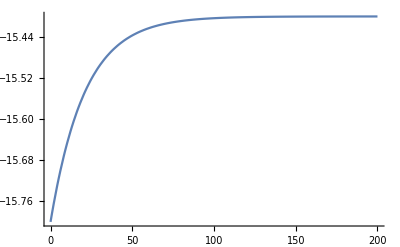

```mathematica
DiffIncorp[f_,xi_,T_] :=
NDSolve[
{xb'[t] == f*xb[t] + (1-f)*xi - xb[t],
xb[0]==-15.8},
xb,{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{f=0.952381,xi=-15.4,T=200},

Traj = Evaluate[xb[t]/.DiffIncorp[f,xi,T]];
Plot[Traj,{t,0,T},PlotRange->All]

]
```

```mathematica
Solve[0 == f*xbstar + (1-f)*xi - xbstar, xbstar]
```

{{xbstar→xi}}

```mathematica
Remove["Global`*"]
```

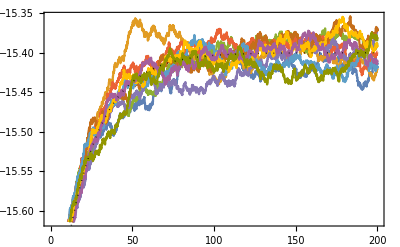

```mathematica
T = 200;
Iterations = 10;
IP[f_,xbar_,sigma_,x0_] := ItoProcess[
ⅆxb[t]==f*xb[t]*ⅆt+(1-f)*(xbar*ⅆt + sigma*ⅆw[t]) - xb[t]*ⅆt,
xb[t],{xb,x0},t,w\[Distributed]WienerProcess[]];
stochsol[f_,xbar_,sigma_,x0_] :=
RandomFunction[IP[f,xbar,sigma,x0],{0,T,0.05},Iterations,Method-> "KloedenPlatenSchurz"];

With[{f=0.952381,xbar=-15.4,sigma =0.1,x0=-15.8},
TD = stochsol[f,xbar,sigma,x0]["PathComponents"];
Show[{
ListLinePlot[stochsol[f,xbar,sigma,x0],Frame->True],
Plot[ⅇ^((-1+f) t) (x0-xbar)+xbar,{t,0,T},PlotRange->All,PlotStyle->{Black,Thick,Dotted}]
}]
]
```

```mathematica
ExpIP = Mean[IP[f,xbar,sigma,x0][t]]
VarIP = Variance[IP[f,xbar,sigma,x0][t]]
```

ⅇ^((-1+f) t) (x0-xbar)+xbar

1/2 (-1+ⅇ^(2 (-1+f) t)) (-1+f) sigma^2

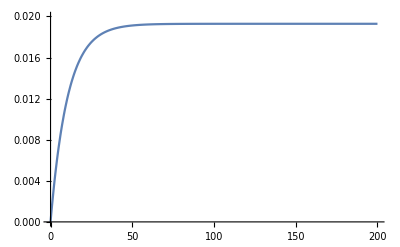

```mathematica
With[{f=0.952381,sigma=0.9},
Plot[1/2 (-1+ⅇ^(2 (-1+f) t)) (-1+f) sigma^2,{t,0,T},PlotRange->{0,0.02}]
]
```

```mathematica
Limit[ExpIP/.{f->0.952381},t -> Infinity]
```

xbar

```mathematica
Limit[VarIP/.{f->0.952381},t->Infinity]
```

0.0238095 sigma^2

```mathematica
Sqrt[%]
```

0.138873

The dirichlet density is only for the K-1 components of the vector, where X_k = 1 - sum_{i=1}^{K-1} X_i

```mathematica
Manipulate[
params = {1,A,1,1,1,1};
Plot3D[PDF[MarginalDistribution[DirichletDistribution[params],{2,3}],{x,y}],{x,0,1},{y,0,1},PlotRange->All],
{A,1,100}]
```

```mathematica
S=Join[R=RandomVariate[DirichletDistribution[params]],{1-Total[R]}]
Total[S]
```

{0.28139,0.511584,0.207026}

1.

```mathematica
sample=RandomVariate[𝒹=DirichletDistribution[params],10^4];
```

```mathematica
Histogram3D[sample,20,"PDF",ColorFunction->"Rainbow"]
```

Histogram3D::ldata: {{0.00601633, 0.499399, 0.0077262, 0.00294612, 0.00217127}, {0.00183805, 0.563937, 0.00395695, 0.0045617, 0.00341696}, {0.00132857, 0.525683, 0.00508636, 0.00487025, 0.00238833}, « 45 », {0.00402656, 0.46236, 0.000916694, 0.00705978, 0.00185517}, {0.0050099, 0.523309, 0.00187827, 0.00476714, 0.00084479}, « 9950 »} is not a valid dataset or list of datasets.

1
 |  |  |  |

```mathematica
sample=RandomVariate[DirichletDistribution[{2,3,1,4}],10];
```

```mathematica
sample
```

{{0.136949,0.3124,0.0397252},{0.238335,0.127092,0.117571},{0.107395,0.554802,0.0839272},{0.266623,0.0725864,0.0358234},{0.167436,0.254607,0.269122},{0.402321,0.165108,0.0759411},{0.357838,0.102962,0.0287242},{0.19351,0.40699,0.108165},{0.0948545,0.735079,0.00280517},{0.378454,0.17001,0.110127}}

```mathematica
SampleProp = Table[{0.5,0.2,0},{500}];
edist=EstimatedDistribution[SampleProp, DirichletDistribution[{α1,α2,α3,α4}]]
```

DirichletDistribution[{0.,0.,0.,0.}]

```mathematica
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
Dparam = {2,2,2,10,10,1,1,1,1,1,1,1};
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
```

```mathematica
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]]
```

0.213656

```mathematica
Sqrt[%]
```

0.462229

```mathematica
Covp//MatrixForm
```

(0. | -0.000108032 | -0.000108032 | -0.000540161 | -0.000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161
-0.000108032 | 0. | -0.000108032 | -0.000540161 | -0.000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161
-0.000108032 | -0.000108032 | 0. | -0.000540161 | -0.000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161 | -0.0000540161
-0.000540161 | -0.000540161 | -0.000540161 | 0. | -0.0027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008
-0.000540161 | -0.000540161 | -0.000540161 | -0.0027008 | 0. | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008 | -0.00027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | 0. | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | 0. | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | -0.000027008 | 0. | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | -0.000027008 | -0.000027008 | 0. | -0.000027008 | -0.000027008 | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | 0. | -0.000027008 | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | 0. | -0.000027008
-0.0000540161 | -0.0000540161 | -0.0000540161 | -0.00027008 | -0.00027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | -0.000027008 | 0.)

```mathematica
a0
```

30

```mathematica
Remove[a0]
Remove[EX]
Remove[VarX]
VarZAnalytic = N[Sum[((Subscript[a,i]*(a0-Subscript[a,i]))/(a0^2*(a0+1)))*Subscript[VarX,i] + (Subscript[a,i]/a0)^2*Subscript[VarX,i] + Subscript[EX,i]^2*((Subscript[a,i]*(a0-Subscript[a,i]))/(a0^2*(a0+1))) + Sum[((-Subscript[a,i]*Subscript[a,j])/(a0^2*(a0+1))Boole[i ≠ j])*Subscript[EX,i]*Subscript[EX,j]Boole[i ≠ j],{j,1,Infinity}],{i,1,Infinity}]]
```

$Aborted

```mathematica
FullSimplify[VarZAnalytic]
```

1/(a0^2 (1.+a0))(a0 a_3 EX_3^2-1. a_3^2 EX_3^2-2. a_3 a_4 EX_3 EX_4+a0 a_4 EX_4^2-1. a_4^2 EX_4^2-2. a_3 a_5 EX_3 EX_5-2. a_4 a_5 EX_4 EX_5+a0 a_5 EX_5^2-1. a_5^2 EX_5^2-2. a_3 a_6 EX_3 EX_6-2. a_4 a_6 EX_4 EX_6-2. a_5 a_6 EX_5 EX_6+a0 a_6 EX_6^2-1. a_6^2 EX_6^2-2. a_3 a_7 EX_3 EX_7-2. a_4 a_7 EX_4 EX_7-2. a_5 a_7 EX_5 EX_7-2. a_6 a_7 EX_6 EX_7+a0 a_7 EX_7^2-1. a_7^2 EX_7^2-2. a_3 a_8 EX_3 EX_8-2. a_4 a_8 EX_4 EX_8-2. a_5 a_8 EX_5 EX_8-2. a_6 a_8 EX_6 EX_8-2. a_7 a_8 EX_7 EX_8+a0 a_8 EX_8^2-1. a_8^2 EX_8^2-2. a_3 a_9 EX_3 EX_9-2. a_4 a_9 EX_4 EX_9-2. a_5 a_9 EX_5 EX_9-2. a_6 a_9 EX_6 EX_9-2. a_7 a_9 EX_7 EX_9-2. a_8 a_9 EX_8 EX_9+a0 a_9 EX_9^2-1. a_9^2 EX_9^2-2. a_3 a_10 EX_3 EX_10-2. a_4 a_10 EX_4 EX_10-2. a_5 a_10 EX_5 EX_10-2. a_6 a_10 EX_6 EX_10-2. a_7 a_10 EX_7 EX_10-2. a_8 a_10 EX_8 EX_10-2. a_9 a_10 EX_9 EX_10+a0 a_10 EX_10^2-1. a_10^2 EX_10^2-2. a_3 a_11 EX_3 EX_11-2. a_4 a_11 EX_4 EX_11-2. a_5 a_11 EX_5 EX_11-2. a_6 a_11 EX_6 EX_11-2. a_7 a_11 EX_7 EX_11-2. a_8 a_11 EX_8 EX_11-2. a_9 a_11 EX_9 EX_11-2. a_10 a_11 EX_10 EX_11+a0 a_11 EX_11^2-1. a_11^2 EX_11^2-2. a_3 a_12 EX_3 EX_12-2. a_4 a_12 EX_4 EX_12-2. a_5 a_12 EX_5 EX_12-2. a_6 a_12 EX_6 EX_12-2. a_7 a_12 EX_7 EX_12-2. a_8 a_12 EX_8 EX_12-2. a_9 a_12 EX_9 EX_12-2. a_10 a_12 EX_10 EX_12-2. a_11 a_12 EX_11 EX_12+a0 a_12 EX_12^2-1. a_12^2 EX_12^2+a_1^2 (-1. EX_1^2+a0 VarX_1)+a_1 (a0 EX_1^2+EX_1 (-2. a_2 EX_2-2. a_3 EX_3-2. a_4 EX_4-2. a_5 EX_5-2. a_6 EX_6-2. a_7 EX_7-2. a_8 EX_8-2. a_9 EX_9-2. a_10 EX_10-2. a_11 EX_11-2. a_12 EX_12)+a0 VarX_1)+a_2^2 (-1. EX_2^2+a0 VarX_2)+a_2 (a0 EX_2^2+EX_2 (-2. a_3 EX_3-2. a_4 EX_4-2. a_5 EX_5-2. a_6 EX_6-2. a_7 EX_7-2. a_8 EX_8-2. a_9 EX_9-2. a_10 EX_10-2. a_11 EX_11-2. a_12 EX_12)+a0 VarX_2)+a0 a_3 VarX_3+a0 a_3^2 VarX_3+a0 a_4 VarX_4+a0 a_4^2 VarX_4+a0 a_5 VarX_5+a0 a_5^2 VarX_5+a0 a_6 VarX_6+a0 a_6^2 VarX_6+a0 a_7 VarX_7+a0 a_7^2 VarX_7+a0 a_8 VarX_8+a0 a_8^2 VarX_8+a0 a_9 VarX_9+a0 a_9^2 VarX_9+a0 a_10 VarX_10+a0 a_10^2 VarX_10+a0 a_11 VarX_11+a0 a_11^2 VarX_11+a0 a_12 (1+a_12) VarX_12)

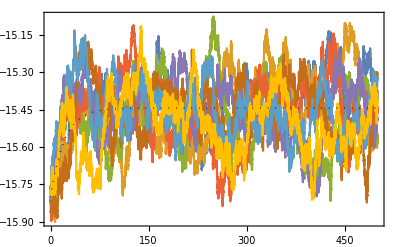

```mathematica
Remove["Global`*"]
T = 500;
Iterations = 8;
IP[f_,xbar_,sigma_,x0_] := ItoProcess[
ⅆxb[t]==f*xb[t]*ⅆt+(1-f)*(xbar*ⅆt + sigma*ⅆw[t]) - xb[t]*ⅆt,
xb[t],{xb,x0},t,w\[Distributed]WienerProcess[]];
stochsol[f_,xbar_,sigma_,x0_] :=
RandomFunction[IP[f,xbar,sigma,x0],{0,T,0.05},Iterations,Method-> "KloedenPlatenSchurz"];

nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX= {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
a= {1,1,1,1,1,100,1,1,1,1,1,1};
a0 = Total[a];
Ep = N[a/a0];
Varp = N[Table[(a[[i]]*(a0-a[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp =  N[Table[(-a[[i]]*a[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
With[{
f=0.952381,
xbar=N[∑_(i=1)^nprey a[[i]]/a0*EX[[i]]],
sigma = Sqrt[ N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]]],
x0=-15.8},
TD = stochsol[f,xbar,sigma,x0];
Show[{
ListLinePlot[stochsol[f,xbar,sigma,x0],Frame->True],
Plot[ⅇ^((-1+f) t) (x0-xbar)+xbar,{t,0,T},PlotRange->All,PlotStyle->{Black,Thick,Dotted}]
}]
]
```

```mathematica
TD["PathComponents"]
```

RandomFunction[ItoProcess[{{xbar-f xbar-xb[t]+f xb[t]},{{sigma-f sigma}},xb[t]},{{xb},{x0}},{t,0}],{0,500,0.05},8,Method→KloedenPlatenSchurz][PathComponents]

```mathematica
Histogram[TD[[1]]["Paths"][[1,All]][[All,2]]]
```

Histogram::ldata: String[] is not a valid dataset or list of datasets.

Histogram[String[]]

Analysis of the steady state solutions with respect to the incorporation rate (1-f)

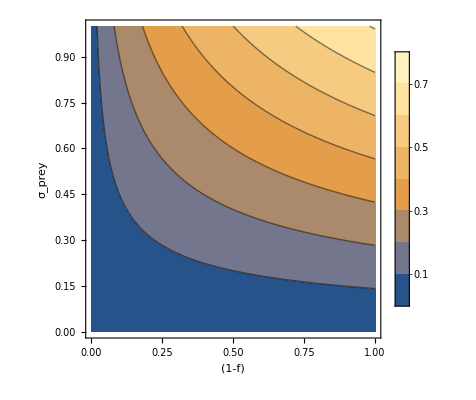

```mathematica
ContourPlot[Sqrt[(1/2)*OneMinusF*sigma^2],{OneMinusF,0,1},{sigma,0,1},FrameLabel->{"(1-f)","σ_prey"},PlotLegends->Automatic]
```

For a population, the distribution will be a mixture of normal distributions that describe the individuals.
The below equations work out explicit forms for the moments of a mixture of normals.

```mathematica
𝒟=MixtureDistribution[{w1,w2,w3,w4},{NormalDistribution[E1,S1],NormalDistribution[E2,S2],NormalDistribution[E3,S3],NormalDistribution[E4,S4]}];
```

```mathematica
PDF[𝒟,x]
```

(ⅇ^(-(-E1+x)^2/(2 S1^2)) w1)/(√(2 π) S1 (w1+w2+w3+w4))+(ⅇ^(-(-E2+x)^2/(2 S2^2)) w2)/(√(2 π) S2 (w1+w2+w3+w4))+(ⅇ^(-(-E3+x)^2/(2 S3^2)) w3)/(√(2 π) S3 (w1+w2+w3+w4))+(ⅇ^(-(-E4+x)^2/(2 S4^2)) w4)/(√(2 π) S4 (w1+w2+w3+w4))

```mathematica
CDF[𝒟,x]
```

(w1 Erfc[(E1-x)/(√2 S1)])/(2 (w1+w2+w3+w4))+(w2 Erfc[(E2-x)/(√2 S2)])/(2 (w1+w2+w3+w4))+(w3 Erfc[(E3-x)/(√2 S3)])/(2 (w1+w2+w3+w4))+(w4 Erfc[(E4-x)/(√2 S4)])/(2 (w1+w2+w3+w4))

```mathematica
Mean[𝒟]
```

1/4 (E1+E2+E3+E4)

```mathematica
Variance[𝒟]
```

1/16 (3 E1^2-2 E1 E2+3 E2^2-2 E1 E3-2 E2 E3+3 E3^2-2 E1 E4-2 E2 E4-2 E3 E4+3 E4^2+4 S1^2+4 S2^2+4 S3^2+4 S4^2)

```mathematica
FullSimplify[%]
```

1/16 (3 E1^2+3 E2^2+3 E3^2-2 E3 E4+3 E4^2-2 E2 (E3+E4)-2 E1 (E2+E3+E4)+4 (S1^2+S2^2+S3^2+S4^2))

```mathematica
FullSimplify[With[{n=4},
1/n^2*(Sum[ n*Subscript[S,i]^2+(n-1)*Subscript[Ex,i]^2 -Sum[Subscript[Ex,i]*Subscript[Ex,j]Boole[i≠j],{j,1,n}] ,{i,1,n}])
]]
```

1/16 (3 Ex_1^2+3 Ex_2^2+3 Ex_3^2-2 Ex_3 Ex_4+3 Ex_4^2-2 Ex_2 (Ex_3+Ex_4)-2 Ex_1 (Ex_2+Ex_3+Ex_4)+4 (S_1^2+S_2^2+S_3^2+S_4^2))

```mathematica
𝒟2=MixtureDistribution[{1,1,1,1},{NormalDistribution[E1,S1],NormalDistribution[E2,S1],NormalDistribution[E3,S1],NormalDistribution[E4,S1]}]
```

MixtureDistribution[{1,1,1,1},{NormalDistribution[E1,S1],NormalDistribution[E2,S1],NormalDistribution[E3,S1],NormalDistribution[E4,S1]}]

```mathematica
PDF[𝒟2]
```

Function[x,(ⅇ^(-(x-E1)^2/(2 S1^2)))/(4 √(2 π) S1)+(ⅇ^(-(x-E2)^2/(2 S1^2)))/(4 √(2 π) S1)+(ⅇ^(-(x-E3)^2/(2 S1^2)))/(4 √(2 π) S1)+(ⅇ^(-(x-E4)^2/(2 S1^2)))/(4 √(2 π) S1)]

```mathematica
Mean[𝒟2]
```

1/4 (E1+E2+E3+E4)

```mathematica
Variance[𝒟2]
```

1/16 (3 E1^2-2 E1 E2+3 E2^2-2 E1 E3-2 E2 E3+3 E3^2-2 E1 E4-2 E2 E4-2 E3 E4+3 E4^2+16 S1^2)